### Coordinate relations

```mathematica
lorentzFactor = 1/(√(1 -v^2));
boostMatrix = ({{lorentzFactor, 0, 0, - v lorentzFactor}, {0, 1, 0, 0}, {0, 0, 1, 0}, {- v lorentzFactor, 0, 0, lorentzFactor}});
inertialCoords[t_] := ({{t}, {x}, {y}, {z}});
boostedCoords[t_] := boostMatrix . inertialCoords[t];
boostedR[t_] := √((boostedCoords[t][[1]])^2+(boostedCoords[t][[2]])^2+(boostedCoords[t][[3]])^2)[[1]];
boostedR[t]
```

√(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)

### Schwarzschild solution in isotropic coordinates

```mathematica
boostedLapse[t_] := (1- M/(2 boostedR[t]))/(1 + M/(2 boostedR[t]));
w[t_] := 1 + M/(2 boostedR[t]);
boostedSpacetimeMetric[t_] := ({{-boostedLapse[t]^2, 0, 0, 0}, {0, w[t]^4, 0, 0}, {0, 0, w[t]^4, 0}, {0, 0, 0, w[t]^4}});
boostedSpacetimeMetric[t] // MatrixForm
```

(-((1-1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2)/((1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2) | 0 | 0 | 0
0 | (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4 | 0 | 0
0 | 0 | (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4 | 0
0 | 0 | 0 | (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4)

### Lorentz boost

```mathematica
spacetimeMetric[t_] := boostMatrix . (boostMatrix . boostedSpacetimeMetric[t]);
spacetimeMetric[t] // MatrixForm
```

(-((1-1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2)/((1-v^2) (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2)-(v^2 (1-1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2)/((1-v^2) (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2) | 0 | 0 | -(2 v (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4)/(1-v^2)
0 | (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4 | 0 | 0
0 | 0 | (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4 | 0
(2 v (1-1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2)/((1-v^2) (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^2) | 0 | 0 | ((1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4)/(1-v^2)+(v^2 (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4)/(1-v^2))

### 3+1 decomposition

```mathematica
spatialMetric[t_]:=({{spacetimeMetric[t][[2,2]], spacetimeMetric[t][[2,3]], spacetimeMetric[t][[2,4]]}, {spacetimeMetric[t][[3,2]], spacetimeMetric[t][[3,3]], spacetimeMetric[t][[3,4]]}, {spacetimeMetric[t][[4,2]], spacetimeMetric[t][[4,3]], spacetimeMetric[t][[4,4]]}});
spatialMetric[t] // MatrixForm
```

((1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4 | 0 | 0
0 | (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4 | 0
0 | 0 | ((1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4)/(1-v^2)+(v^2 (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^4)/(1-v^2))

```mathematica
dtSpatialMetric[t_] := D[spatialMetric[time], time] /. time -> t;
dtSpatialMetric[t] // MatrixForm
```

(-(2 (t/(√(1-v^2))-(v z)/(√(1-v^2))) (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^3)/(√(1-v^2) (x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)^(3/2)) | 0 | 0
0 | -(2 (t/(√(1-v^2))-(v z)/(√(1-v^2))) (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^3)/(√(1-v^2) (x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)^(3/2)) | 0
0 | 0 | -(2 (t/(√(1-v^2))-(v z)/(√(1-v^2))) (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^3)/((1-v^2)^(3/2) (x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)^(3/2))-(2 v^2 (t/(√(1-v^2))-(v z)/(√(1-v^2))) (1+1/(2 √(x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)))^3)/((1-v^2)^(3/2) (x^2+y^2+(t/(√(1-v^2))-(v z)/(√(1-v^2)))^2)^(3/2)))

```mathematica
dtSpatialMetric[0] // MatrixForm
```

((2 v z (1+1/(2 √(x^2+y^2+(v^2 z^2)/(1-v^2))))^3)/((1-v^2) (x^2+y^2+(v^2 z^2)/(1-v^2))^(3/2)) | 0 | 0
0 | (2 v z (1+1/(2 √(x^2+y^2+(v^2 z^2)/(1-v^2))))^3)/((1-v^2) (x^2+y^2+(v^2 z^2)/(1-v^2))^(3/2)) | 0
0 | 0 | (2 v z (1+1/(2 √(x^2+y^2+(v^2 z^2)/(1-v^2))))^3)/((1-v^2)^2 (x^2+y^2+(v^2 z^2)/(1-v^2))^(3/2))+(2 v^3 z (1+1/(2 √(x^2+y^2+(v^2 z^2)/(1-v^2))))^3)/((1-v^2)^2 (x^2+y^2+(v^2 z^2)/(1-v^2))^(3/2)))

### Falloff

```mathematica
falloff[xx_, yy_, zz_] :=  spatialMetric[0] - ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}) /. {x->xx, y->yy, z->zz};
falloff[xx,yy,zz] // MatrixForm
```

(-1+(1+1/(2 √(xx^2+yy^2+(v^2 zz^2)/(1-v^2))))^4 | 0 | 0
0 | -1+(1+1/(2 √(xx^2+yy^2+(v^2 zz^2)/(1-v^2))))^4 | 0
0 | 0 | -1+((1+1/(2 √(xx^2+yy^2+(v^2 zz^2)/(1-v^2))))^4)/(1-v^2)+(v^2 (1+1/(2 √(xx^2+yy^2+(v^2 zz^2)/(1-v^2))))^4)/(1-v^2))

```mathematica
falloff[0, 0, 10] /. v->0.5
```

{{0.394064,0,0},{0,0.394064,0},{0,0,1.32344}}

```mathematica
falloff[r, 0, 0][[1,1]]
```

-1+(1+1/(2 √(r^2)))^4

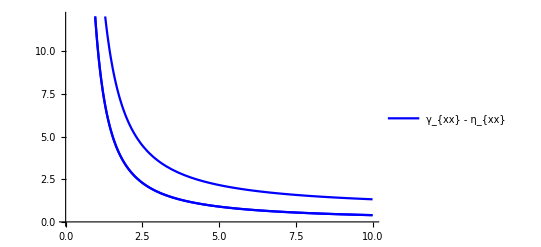

```mathematica
Plot[{
falloff[0, 0, r][[1,1]], falloff[0, 0, r][[2,2]], falloff[0, 0, r][[3,3]]
} /. v->0.5, {r, 0, 10},
PlotStyle->{Red,Green,Blue},
PlotLegends->Placed[{Style["γ_{xx} - η_{xx}",FontSize->12],Style["γ_{yy} - η_{yy}",FontSize->12],Style["γ_{zz} - η_{zz}",FontSize->12]},{Right,Top}]
]
```